```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{100,200,500,10,5000,300}];
Subscript[R, lqr]=DiagonalMatrix[{1,100}];
Subscript[L, 0]=0.20;Subscript[Q, 0]=90;
(*====================系统参数配置====================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.003993;Subscript[J, 2]=0.064379;Subscript[J, 3]=0.060525;Subscript[J, 4]=0.003993;
Subscript[m, 1]=0.211*2;Subscript[m, 2]=0.390*2;Subscript[m, 3]=0.204*2;Subscript[m, 4]=0.211*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.2997272;(*机体的转动惯量*)
Subscript[m, b]=8.548;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000813;
Subscript[m, wm]=0.10*2;(*壳0.1 电机0.38*)
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.63*2;(*驱动轮的质量 0.35*)
Subscript[R, w]=0.06;(*轮的半径*)
(*====================求解等效腿的质量分布====================*)
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[Subscript[L, 0],Subscript[Q, 0],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*====================腿部模型参数传递====================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*====================导入模型====================*)
θ=(Subscript[Q, 0]-90)/180*Pi;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*====================LQR控制====================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr]
```

{{6.08535,12.6636,49.1418,7.57203,54.8073,12.7387},{-0.793527,-1.75976,-13.1544,-1.78789,4.8796,1.66868}}

```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{100,200,500,10,5000,300}];
Subscript[R, lqr]=DiagonalMatrix[{1,100}];
Subscript[L, 0]=0.20;Subscript[Q, 0]=90;
(*====================系统参数配置====================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.003993;Subscript[J, 2]=0.064379;Subscript[J, 3]=0.060525;Subscript[J, 4]=0.003993;
Subscript[m, 1]=0.211*2;Subscript[m, 2]=0.390*2;Subscript[m, 3]=0.204*2;Subscript[m, 4]=0.211*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.2997272;(*机体的转动惯量*)
Subscript[m, b]=8.548;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000813;
Subscript[m, wm]=0.10*2;(*壳0.1 电机0.38*)
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.63*2;(*驱动轮的质量 0.35*)
Subscript[R, w]=0.06;(*轮的半径*)
(*限位*)
upLimit=-23.41;(*上限位*)
downLimit=67.89;(*下限位*)
(*电机半径--画图*)
Subscript[R, jm]=0.045;(*GO8010*)
Subscript[R, wm]=0.0675;(*MF9025*)
(*Save[NotebookDirectory[]<>"\\VMCsolution.m",VMCForwardSolution,VMCInverseSolution];*)
Get["VMCsolution.m",Path->NotebookDirectory[]]
SystemCalcu[L0_,Q0_]:=(
Module[{},
Subscript[L, 0]=L0;
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[L0,Q0,{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*====================求解等效腿的质量分布====================*)
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*====================腿部模型参数传递====================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*====================导入模型====================*)
θ=(Q0-90)/180*Pi;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*====================LQR控制====================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
Return[Subscript[K, lqr]];
];
);
Manipulate[SystemCalcu[L0,Q0],{{L0,0.2},0.1,0.4},{{Q0,90},180,0}](*显示具体数值*)
```

{9.93454-4.78349 x-49.5749 x^2+73.6911 x^3,18.011-17.0877 x-55.0937 x^2+94.3588 x^3,34.2832+183.616 x-790.238 x^2+854.89 x^3,7.46697+5.18589 x-32.1947 x^2+34.5385 x^3,55.9469+106.131 x-54.0832 x^2-87.9729 x^3,10.7002+47.3682 x-56.1761 x^2+11.2716 x^3,-0.976265-1.07592 x-0.586662 x^2+2.68085 x^3,-2.02614+0.0521471 x-7.15447 x^2+10.5053 x^3,-7.1408-46.8898 x+66.44 x^2-45.4585 x^3,-1.61957+0.353914 x-13.8965 x^2+13.0106 x^3,7.72793-9.97756 x-13.7811 x^2+29.7827 x^3,2.92789-6.42717 x+5.36498 x^2-0.454433 x^3}

{{9.93454,-4.78349,-49.5749,73.6911},{18.011,-17.0877,-55.0937,94.3588},{34.2832,183.616,-790.238,854.89},{7.46697,5.18589,-32.1947,34.5385},{55.9469,106.131,-54.0832,-87.9729},{10.7002,47.3682,-56.1761,11.2716},{-0.976265,-1.07592,-0.586662,2.68085},{-2.02614,0.0521471,-7.15447,10.5053},{-7.1408,-46.8898,66.44,-45.4585},{-1.61957,0.353914,-13.8965,13.0106},{7.72793,-9.97756,-13.7811,29.7827},{2.92789,-6.42717,5.36498,-0.454433}}

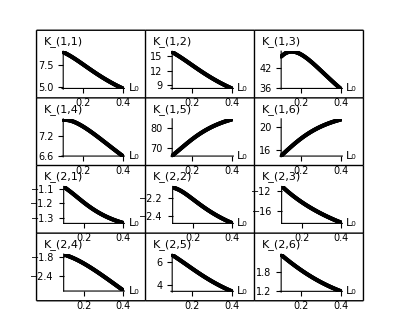

```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{200,250,500,20,8000,500}];
Subscript[R, lqr]=DiagonalMatrix[{1,100}];
Get["VMCsolution.m",Path->NotebookDirectory[]]
(*=============================================系统参数配置=============================================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.003993;Subscript[J, 2]=0.064379;Subscript[J, 3]=0.060525;Subscript[J, 4]=0.003993;
Subscript[m, 1]=0.211*2;Subscript[m, 2]=0.390*2;Subscript[m, 3]=0.204*2;Subscript[m, 4]=0.211*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.2997272;(*机体的转动惯量*)
Subscript[m, b]=8.548;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000813;
Subscript[m, wm]=0.10*2;(*壳0.1 电机0.38*)
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.63*2;(*驱动轮的质量 0.35*)
Subscript[R, w]=0.06;(*轮的半径*)
(*=============================================开始循环迭代============================================*)
sampleNum=101;(*循环次数*)
paramNum=12;(*变量个数*)
Kt=Array[0,{sampleNum}];
Lt=Array[0,{sampleNum}];
Do[
(*输入量控制*)
Subscript[L, 0]=0.10+0.3*(cnt)/sampleNum;
Subscript[Q, 0]=90;
(*=========================================求解等效腿的质量分布====================================*)
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[Subscript[L, 0],Subscript[Q, 0],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*============================================腿部模型参数传递====================================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*============================================导入模型============================================*)
θ=(Subscript[Q, 0]-90)/180*Pi;
α=0;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*============================================LQR控制============================================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
(*============================================数据记录===========================================*)
Kt[[cnt]] = Subscript[K, lqr];
Lt[[cnt]] = Subscript[L, 0];
,{cnt,sampleNum}];
(*============================================多项式拟合============================================*)
(*提取同一参数在不同条件下的值*)
kArray=Array[0,{paramNum}];Do[Do[kArray[[(i-1)*6+j]]=Kt[[All,i,j]],{j,6}],{i,2}];	
(*将条件值与参数值配对*)
Kxy=Array[0,{paramNum,sampleNum}];
Do[Do[Kxy[[i,j]]={Lt[[j]],kArray[[i,j]]},{j,sampleNum}],{i,paramNum}];	
(*分别对各个参数进行多项式拟合*)
Kpoly = Array[0, {paramNum}];
Do[Kpoly[[i]]= Fit[Kxy[[i]],{1,x,x^2,x^3},x],{i,paramNum}];
Kpoly
(*将多项式系数整合成一个矩阵*)
kPolyMatrix = Array[0,{12}];
Do[kPolyMatrix[[i]]=CoefficientList[Kpoly[[i]],x],{i,paramNum}];
(*多项式拟合曲线*)
KT = Array[0, {paramNum}];
Do[KT[[plotcnt]] = Plot[Kpoly[[plotcnt]], {x, Lt[[1]], Lt[[sampleNum]]}, Epilog->Point[Kxy[[plotcnt]]],Axes->{True,True}, AxesLabel->{"L_0", Subscript[K, 1,plotcnt]}],{plotcnt, 1, 6}];
Do[KT[[plotcnt]] = Plot[Kpoly[[plotcnt]], {x, Lt[[1]], Lt[[sampleNum]]}, Epilog->Point[Kxy[[plotcnt]]],Axes->{True,True}, AxesLabel->{"L_0", Subscript[K, 2,plotcnt-6]}],{plotcnt, 7, 12}];
KL0Graph = GraphicsGrid[{{KT [[1]],KT [[2]],KT [[3]]},{KT [[4]],KT [[5]],KT [[6]]},
	{KT [[7]],KT [[8]],KT [[9]]},{KT [[10]],KT [[11]],KT [[12]]}}, Frame->All,ImageSize->Full];
(*============================================数据输出===========================================*)
Print[kPolyMatrix];(*拟合多项式升幂排列*)
Show[KL0Graph](*多项式拟合曲线图*)
```

```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{200,250,500,20,8000,500}];
Subscript[R, lqr]=DiagonalMatrix[{1,100}];
Get["VMCsolution.m",Path->NotebookDirectory[]]
(*=============================================系统参数配置=============================================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.003993;Subscript[J, 2]=0.064379;Subscript[J, 3]=0.060525;Subscript[J, 4]=0.003993;
Subscript[m, 1]=0.211*2;Subscript[m, 2]=0.390*2;Subscript[m, 3]=0.204*2;Subscript[m, 4]=0.211*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.2997272;(*机体的转动惯量*)
Subscript[m, b]=8.548;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000813;
Subscript[m, wm]=0.10*2;(*壳0.1 电机0.38*)
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.63*2;(*驱动轮的质量 0.35*)
Subscript[R, w]=0.06;(*轮的半径*)
(*=============================================开始循环迭代============================================*)
sampleNum=51;(*循环次数*)
paramNum=12;(*变量个数*)
Kt=Array[0,{sampleNum,sampleNum}];
Xt=Array[0,{sampleNum,sampleNum}];
Do[
Do[
(*输入量控制*)
Subscript[L, 0]=0.10+0.2*(cnt1)/sampleNum;
Subscript[Q, 0]=40+100*(cnt2)/sampleNum;
(*=========================================求解等效腿的质量分布====================================*)
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[Subscript[L, 0],Subscript[Q, 0],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*============================================腿部模型参数传递====================================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*============================================导入模型============================================*)
θ=(Subscript[Q, 0]-90)/180*Pi;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*============================================LQR控制============================================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
(*============================================数据记录===========================================*)
Kt[[cnt1,cnt2]] = Subscript[K, lqr];
Xt[[cnt1,cnt2]]={Subscript[L, 0],Subscript[Q, 0]};
,{cnt1,sampleNum}];
,{cnt2,sampleNum}];
(*============================================多项式拟合============================================*)
(*提取同一参数在不同条件下的值*)
kArray=Array[0,{paramNum}];Do[Do[kArray[[(i-1)*6+j]]=Kt[[All,All,i,j]],{j,6}],{i,2}];
(*将条件值与参数值配对*)
Kxy=Array[0,{paramNum,sampleNum*sampleNum}];
Do[Do[Do[Kxy[[i,(j-1)*sampleNum+k]]={Xt[[j,k,1]],Xt[[j,k,2]],kArray[[i,j,k]]},{k,sampleNum}],{j,sampleNum}],{i,paramNum}];
(*分别对各个参数进行多项式拟合*)
Kpoly = Array[0, {paramNum}];
Do[Kpoly[[i]]= Fit[Kxy[[i]],{1,x,x^2,x^3,y,y^2,y^3,x*y,x^2*y,x*y^2},{x,y}],{i,paramNum}];
Kpoly
(*将多项式系数整合成一个矩阵*)
kPolyMatrix = Array[0,{12}];
Do[kPolyMatrix[[i]]=CoefficientList[Kpoly[[i]],{x,y}],{i,paramNum}];
(*多项式拟合曲线*)
KT = Array[0, {paramNum}];
KTT=Array[0,{paramNum}];
Do[KT[[plotcnt]] = Plot3D[Kpoly[[plotcnt]], {x, Xt[[1,1,1]], Xt[[sampleNum,sampleNum,1]]},{y, Xt[[1,1,2]], Xt[[sampleNum,sampleNum,2]]},Axes->{True,True,True}, AxesLabel->{"L_0", "Q_0",Subscript[K, 1,plotcnt]}];
KTT[[plotcnt]]=ListPlot3D[Kxy[[plotcnt]]],{plotcnt, 1, 6}];
Do[KT[[plotcnt]] = Plot3D[Kpoly[[plotcnt]],{x, Xt[[1,1,1]], Xt[[sampleNum,sampleNum,1]]},{y, Xt[[1,1,2]], Xt[[sampleNum,sampleNum,2]]}, Axes->{True,True,True}, AxesLabel->{"L_0", "Q_0",Subscript[K, 2,plotcnt-6]}];
KTT[[plotcnt]]=ListPlot3D[Kxy[[plotcnt]]],{plotcnt, 7, 12}];
(*KL0Graph = GraphicsGrid[{{KT[[1]],KT[[2]],KT[[3]]},{KT[[4]],KT[[5]],KT[[6]]},
	{KT[[7]],KT[[8]],KT[[9]]},{KT[[10]],KT[[11]],KT[[12]]}}, Frame->All,ImageSize->Full];*)
KLTGraph = GraphicsGrid[{{KT[[1]],KTT[[1]],KT[[2]],KTT[[2]]},{KT[[3]],KTT[[3]],KT[[4]],KTT[[4]]},{KT[[5]],KTT[[5]],KT[[6]],KTT[[6]]},{KT[[7]],KTT[[7]],KT[[8]],KTT[[8]]},{KT[[9]],KTT[[9]],KT[[10]],KTT[[10]]},{KT[[11]],KTT[[11]],KT[[12]],KTT[[12]]}}, Frame->All,ImageSize->Full];
(*============================================数据输出===========================================*)
Print[kPolyMatrix];(*拟合多项式升幂排列*)
Show[KLTGraph]
(*多项式拟合曲线图*)
```

{4.7087-28.0204 x-56.6185 x^2+112.515 x^3+0.141274 y+0.40143 x y+0.0784622 x^2 y-0.000962769 y^2-0.0023947 x y^2+1.36206×10^-6 y^3,7.17705-66.2286 x+5.8847 x^2+47.0187 x^3+0.307745 y+0.553269 x y+0.158318 x^2 y-0.00206142 y^2-0.00341108 x y^2+2.70471×10^-6 y^3,-21.8196-80.3436 x-670.733 x^2+995.026 x^3+1.58107 y+3.69808 x y+0.426098 x^2 y-0.0110047 y^2-0.0213159 x y^2+0.0000161347 y^3,5.00812-42.9151 x+28.6617 x^2-42.935 x^3+0.0995982 y+0.660686 x y+0.0922979 x^2 y-0.000772778 y^2-0.00385128 x y^2+1.65838×10^-6 y^3,94.0735+133.635 x-331.72 x^2+230.401 x^3-1.02142 y+1.17394 x y-0.324255 x^2 y+0.006405 y^2-0.00577817 x y^2-5.68319×10^-6 y^3,21.1366+68.9534 x-181.404 x^2+175.295 x^3-0.298077 y+0.252046 x y-0.13502 x^2 y+0.00189146 y^2-0.00109136 x y^2-1.87857×10^-6 y^3,-1.51513-1.21593 x+1.35252 x^2+1.44274 x^3+0.0139221 y-0.0135415 x y+0.00392049 x^2 y-0.0000874833 y^2+0.0000663689 x y^2+7.77953×10^-8 y^3,-2.83479+0.604203 x-17.2328 x^2+28.7394 x^3+0.0164206 y+0.0256778 x y-0.00125662 x^2 y-0.000101533 y^2-0.000140393 x y^2+7.185×10^-8 y^3,-4.47738+54.0809 x+85.2606 x^2-97.6142 x^3-0.106048 y-2.10507 x y-0.0466696 x^2 y+0.00105777 y^2+0.0117189 x y^2-3.2855×10^-6 y^3,-2.07197-0.841234 x-34.7815 x^2+46.9729 x^3+0.00318767 y+0.123583 x y-0.0105598 x^2 y-7.80634×10^-6 y^2-0.00066989 x y^2-7.71736×10^-8 y^3,4.88035-35.9925 x+17.9988 x^2-1.76811 x^3+0.0919061 y+0.328582 x y+0.0754478 x^2 y-0.000639694 y^2-0.00198781 x y^2+1.01811×10^-6 y^3,3.00566-15.6899 x+23.7715 x^2-26.2856 x^3+0.00844127 y+0.0973122 x y+0.0288295 x^2 y-0.0000814119 y^2-0.000603877 x y^2+2.85729×10^-7 y^3}

{{{4.7087,0.141274,-0.000962769,1.36206×10^-6},{-28.0204,0.40143,-0.0023947,0},{-56.6185,0.0784622,0,0},{112.515,0,0,0}},{{7.17705,0.307745,-0.00206142,2.70471×10^-6},{-66.2286,0.553269,-0.00341108,0},{5.8847,0.158318,0,0},{47.0187,0,0,0}},{{-21.8196,1.58107,-0.0110047,0.0000161347},{-80.3436,3.69808,-0.0213159,0},{-670.733,0.426098,0,0},{995.026,0,0,0}},{{5.00812,0.0995982,-0.000772778,1.65838×10^-6},{-42.9151,0.660686,-0.00385128,0},{28.6617,0.0922979,0,0},{-42.935,0,0,0}},{{94.0735,-1.02142,0.006405,-5.68319×10^-6},{133.635,1.17394,-0.00577817,0},{-331.72,-0.324255,0,0},{230.401,0,0,0}},{{21.1366,-0.298077,0.00189146,-1.87857×10^-6},{68.9534,0.252046,-0.00109136,0},{-181.404,-0.13502,0,0},{175.295,0,0,0}},{{-1.51513,0.0139221,-0.0000874833,7.77953×10^-8},{-1.21593,-0.0135415,0.0000663689,0},{1.35252,0.00392049,0,0},{1.44274,0,0,0}},{{-2.83479,0.0164206,-0.000101533,7.185×10^-8},{0.604203,0.0256778,-0.000140393,0},{-17.2328,-0.00125662,0,0},{28.7394,0,0,0}},{{-4.47738,-0.106048,0.00105777,-3.2855×10^-6},{54.0809,-2.10507,0.0117189,0},{85.2606,-0.0466696,0,0},{-97.6142,0,0,0}},{{-2.07197,0.00318767,-7.80634×10^-6,-7.71736×10^-8},{-0.841234,0.123583,-0.00066989,0},{-34.7815,-0.0105598,0,0},{46.9729,0,0,0}},{{4.88035,0.0919061,-0.000639694,1.01811×10^-6},{-35.9925,0.328582,-0.00198781,0},{17.9988,0.0754478,0,0},{-1.76811,0,0,0}},{{3.00566,0.00844127,-0.0000814119,2.85729×10^-7},{-15.6899,0.0973122,-0.000603877,0},{23.7715,0.0288295,0,0},{-26.2856,0,0,0}}}

-Graphics-

5139.86-429.243 x-6.77124 x^2+0.241432 x^3

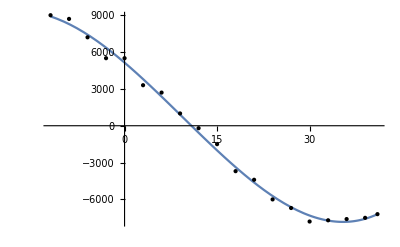

```mathematica
xy={{-12,9000},{-9,8700},{-6,7200},{-3,5500},{0,5500},{3,3300},{6,2700},{9,1000},{12,-200},{15,-1500},{18,-3700},{21,-4400},{24,-6000},{27,-6700},{30,-7800},{33,-7700},{36,-7600},{39,-7500},{41,-7200}};
kploy=Fit[xy,{1,x,x^2,x^3},{x}]
Plot[kploy,{x,-12,41}, Epilog->Point[xy],Axes->{True,True}]
```

```mathematica
(*LQR权重矩阵*)
Subscript[Q, lqr]=DiagonalMatrix[{100,200,500,10,5000,300}];
Subscript[R, lqr]=DiagonalMatrix[{1,100}];
Subscript[L, 0]=0.20;Subscript[Q, 0]=90;
(*====================系统参数配置====================*)
(*重力加速度*)
g=9.81;
(*连杆长度*)
Subscript[L, 1]=0.150;Subscript[L, 2]=0.270;Subscript[L, 3]=0.270;Subscript[L, 4]=0.150;Subscript[L, 5]=0.150;
(*五连杆的质量分布参数*)
Subscript[l, 1]=0.064820;Subscript[l, 2]=0.135660;Subscript[l, 3]=0.135150;Subscript[l, 4]=0.064820;
Subscript[J, 1]=0.003993;Subscript[J, 2]=0.064379;Subscript[J, 3]=0.060525;Subscript[J, 4]=0.003993;
Subscript[m, 1]=0.211*2;Subscript[m, 2]=0.390*2;Subscript[m, 3]=0.204*2;Subscript[m, 4]=0.211*2;
(*机体的质量分布参数*)
Subscript[L, b]=0.01;(*机体质心相对于关节电机轴平面的高度*)
Subscript[J, b]=0.2997272;(*机体的转动惯量*)
Subscript[m, b]=8.548;(*机体的质量*)
(*驱动轮电机的质量分布参数*)
Subscript[J, wm]=0.000813;
Subscript[m, wm]=0.10*2;(*壳0.1 电机0.38*)
(*驱动轮的质量分布参数*)
Subscript[J, w]=0.004301;(*轮子的转动惯量*)
Subscript[m, w]=0.63*2;(*驱动轮的质量 0.35*)
Subscript[R, w]=0.06;(*轮的半径*)
(*限位*)
upLimit=-23.41;(*上限位*)
downLimit=67.89;(*下限位*)
(*电机半径--画图*)
Subscript[R, jm]=0.045;(*GO8010*)
Subscript[R, wm]=0.0675;(*MF9025*)
Get["VMCsolution.m",Path->NotebookDirectory[]]
SystemCalcu[Q1_,Q2_,Q3_,Q4_,Q5_,Q6_,R1_,R2_]:=(
Module[{},
Subscript[Q, lqr]=DiagonalMatrix[{Q1,Q2,Q3,Q4,Q5,Q6}];
Subscript[R, lqr]=DiagonalMatrix[{R1,R2}];
{Subscript[q, 0],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4]}=VMCInverseSolution[Subscript[L, 0],Subscript[Q, 0],{Subscript[L, 1],Subscript[L, 2],Subscript[L, 3],Subscript[L, 4],Subscript[L, 5]}][[3]];
(*====================求解等效腿的质量分布====================*)
(*得各质心矢量*)
Subscript[r, 1]={Subscript[l, 1] Cos[Subscript[q, 1]],Subscript[l, 1] Sin[Subscript[q, 1]]};
Subscript[r, 2]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[l, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[l, 2] Sin[Subscript[q, 2]]};
Subscript[r, 3]={Subscript[L, 4] Cos[Subscript[q, 4]]+Subscript[l, 3] Cos[Subscript[q, 3]]+Subscript[L, 5],Subscript[L, 4] Sin[Subscript[q, 4]]+Subscript[l, 3] Sin[Subscript[q, 3]]};
Subscript[r, 4]={Subscript[l, 4] Cos[Subscript[q, 4]]+Subscript[L, 5],Subscript[l, 4] Sin[Subscript[q, 4]]};
Subscript[r, w]={Subscript[L, 1] Cos[Subscript[q, 1]]+Subscript[L, 2] Cos[Subscript[q, 2]],Subscript[L, 1] Sin[Subscript[q, 1]]+Subscript[L, 2] Sin[Subscript[q, 2]]};
Subscript[m, l]=Subscript[m, 1]+Subscript[m, 2]+Subscript[m, 3]+Subscript[m, 4]+Subscript[m, wm];
M=Subscript[m, l]+Subscript[m, w]+Subscript[m, b];
Subscript[r, com]=Collect[Expand[Subscript[m, 1] Subscript[r, 1]+Subscript[m, 2] Subscript[r, 2]+Subscript[m, 3] Subscript[r, 3]+Subscript[m, 4] Subscript[r, 4]+Subscript[m, wm] Subscript[r, w]],{Cos[Subscript[q, 1]],Sin[Subscript[q, 1]],Cos[Subscript[q, 2]],Sin[Subscript[q, 2]],Cos[Subscript[q, 3]],Sin[Subscript[q, 3]],Cos[Subscript[q, 4]],Sin[Subscript[q, 4]]}]/Subscript[m, l];
(*求解转动惯量*)
Subscript[d, c1]=Norm[Subscript[r, 1]-Subscript[r, com]];Subscript[J, c1]=Subscript[J, 1]+Subscript[m, 1] Subscript[d, c1]^2;
Subscript[d, c2]=Norm[Subscript[r, 2]-Subscript[r, com]];Subscript[J, c2]=Subscript[J, 2]+Subscript[m, 2] Subscript[d, c2]^2;
Subscript[d, c3]=Norm[Subscript[r, 3]-Subscript[r, com]];Subscript[J, c3]=Subscript[J, 3]+Subscript[m, 3] Subscript[d, c3]^2;
Subscript[d, c4]=Norm[Subscript[r, 4]-Subscript[r, com]];Subscript[J, c4]=Subscript[J, 4]+Subscript[m, 4] Subscript[d, c4]^2;
Subscript[d, cwm]=Norm[Subscript[r, w]-Subscript[r, com]];Subscript[J, cwm]=Subscript[J, wm]+Subscript[m, wm] Subscript[d, cwm]^2;
Subscript[J, com]=Subscript[J, c1]+Subscript[J, c2]+Subscript[J, c3]+Subscript[J, c4]+Subscript[J, cwm];
(*====================腿部模型参数传递====================*)
Subscript[J, l]=Subscript[J, com];
Subscript[L, l]=Subscript[L, 0]-Norm[Subscript[r, com]-{Subscript[L, 5]/2,0}];(*腿的质心的高度*)
(*====================导入模型====================*)
θ=(Subscript[Q, 0]-90)/180*Pi;
Subscript[A, op] = Import[NotebookDirectory[]<>"A_op.wdx"];
Subscript[B, op] = Import[NotebookDirectory[]<>"B_op.wdx"];
Subscript[C, op] = DiagonalMatrix[{1,1,1,1,1,1}];
Subscript[D, op] = ConstantArray[0,{6,2}];
(*====================LQR控制====================*)
Subscript[P, lqr] = RiccatiSolve[{Subscript[A, op],Subscript[B, op]},{Subscript[Q, lqr],Subscript[R, lqr]}];(*求解黎卡提方程*)
Subscript[K, lqr] = Inverse[Subscript[R, lqr]].Subscript[B, op] ᵀ.Subscript[P, lqr];
Return[Subscript[K, lqr]];
];
);
Manipulate[SystemCalcu[Q1,Q2,Q3,Q4,Q5,Q6,R1,R2],{{Q1,1},0,10000},{{Q2,1},0,10000},{{Q3,1},0,1000},{{Q4,1},0,1000},{{Q5,1},0,1000000},{{Q6,1},0,1000},{{R1,1},0,1},{{R2,1},0,1000}](*显示具体数值*)
```